```mathematica
sig[x_]:=1/(1+E^(-x))
```

```mathematica
nn[x_,θ_,f_:Tanh]:=Module[{w11,w12,w13,w14,w21,w22,w23},
{w11,w12,w13,w14,w21,w22,w23} = θ;
Return[f[w21*f[w11*x+w12]+w22*f[w13*x+w14]+w23]];
 Return[f[w21*f[w11*f[x]+w12]+w22*f[w13*f[x]+w14]+w23]];
Return[w21*f[w11*x+w12]+w22*f[w13*x+w14]+w23];
]
```

```mathematica
gradient[x_,weights_,fn_:Tanh]:=Module[{w11,w12,w13,w14,w21,w22,w23,w,d},
w={w11,w12,w13,w14,w21,w22,w23};
d=D[nn[x,w,fn],{w}]/.MapThread[#1->#2&,{w,weights}];
Return[d]
]
```

```mathematica
D[-1/2(y-nn[x,{w11,w12,w13,w14,w21,w22,w23},f])^2,{{w11,w12,w13,w14,w21,w22,w23}}]//TableForm
```

w21 x (y-f[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]) f'[w12+w11 x] f'[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]
w21 (y-f[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]) f'[w12+w11 x] f'[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]
w22 x (y-f[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]) f'[w14+w13 x] f'[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]
w22 (y-f[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]) f'[w14+w13 x] f'[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]
f[w12+w11 x] (y-f[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]) f'[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]
f[w14+w13 x] (y-f[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]) f'[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]
(y-f[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]) f'[w23+w21 f[w12+w11 x]+w22 f[w14+w13 x]]

```mathematica
({x2,x3}-{y2,y3})^2
```

{x2-y2,x3-y3}

```mathematica
(*
Implement a simple backpropagation algorithm and print out the
weights along the way. Use this to really understand what is 
going on. And then use it as a way to generate data to test your
software with. Eg, you can generate the entire sequience of weights,
 outputs, and errors for 10, 100, or even 1000 iterations of 
backpropagation and use that to verify your python program.
*)
```

```mathematica
train[data_,init_,lr_:.1,epochs_:100]:=Module[{θ,errors,adjust,batches},
θ=init;
Do[
errors = Map[d↦{d[[1]],d[[2]]-nn[d[[1]],θ]},data];
adjust =Table[θ +=gradient[e[[1]],θ]*e[[2]]*lr,{e,errors}];
(*,{e,RandomSample[errors,10]}]*)
(* θ += Mean@adjust *)
,{epochs}]
Return[θ];
]
```

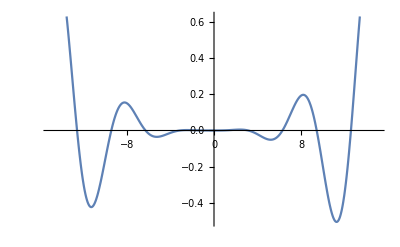

```mathematica
Plot[(x+x^2+x^3)*Sin[x]/3000,{x,-15,15}]
```

```mathematica
data={{2,.9},{1,.3},{-1,.4},{-2,.1}};
data2=Table[{x,(x+x^2+x^3)*Sin[x]/4000},{x,-15,15,.5}];
θ = {.4,-.2,.6,.1,.4,-.2,.6};
```

{0.44548,-8.1177,0.211708,3.06551,1.40588,-0.306272,1.52515}

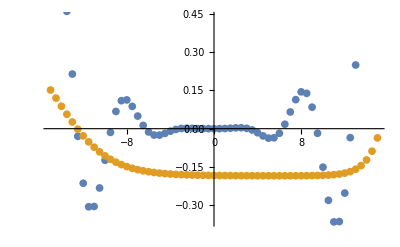

```mathematica
nθ = train[data2, θ,.01,10000]
nnData =Map[in ↦{in, nn[in,nθ]},data2[[All,1]]];
ListPlot[{data2,nnData}]
```

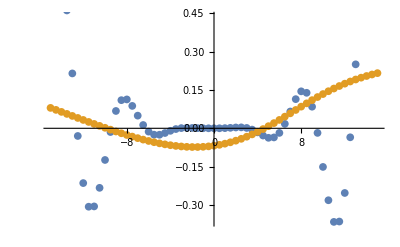

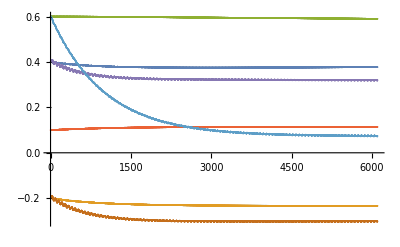

```mathematica
ListPlot[θsᵀ]
```

```mathematica
NonlinearModelFit[data,a+b*x+c*x^2+d*x^3,{a,b,c,d},x]
```

FittedModel[0.3-0.133333 x+0.05 x^2+0.0833333 x^3]

```mathematica
(* Create a general neural network structure generator. That can be
used to graph the network, produce partial derivative table, and other metadata. *)
NODES = "nodes";
ACTIVATION = "activation";
BIASED = "biased";
INPUT="x";
WEIGHT="w";
OUTPUT="y";
COMPILEDNN="compiledNN";
SYMBOLICNN="symbolicNN";
WEIGHTVECTOR="weightVector";
nnConfig={
<|NODES->1,ACTIVATION->Symbol["in"],BIASED->True|>,
<|NODES->4,ACTIVATION->Symbol["hid"],BIASED->True|>,
<|NODES->1,ACTIVATION->Symbol["out"],BIASED->False|>
};
```

{w1¸1,w1¸2,w1¸3,w1¸4,w1¸5,w1¸6,w2¸1,w2¸10,w2¸11,w2¸12,w2¸2,w2¸3,w2¸4,w2¸5,w2¸6,w2¸7,w2¸8,w2¸9,w3¸1,w3¸2,w3¸3,w3¸4}

```mathematica
{.4,-.2,.6,.1,.4,-.2,.6}+Total[{{.4,-.2,.6,.1,.4,-.2,.6}}]
```

{0.8,-0.4,1.2,0.2,0.8,-0.4,1.2}

```mathematica
(* 
At this point we are ready to create a Compiled Module Function that
 takes in the training data, nnConfig, some stoping condition, 
and trains the neural network using gradient decent.
*)
cNN=NeuralNetwork[nnConfig];
cGrad=CompiledGradients[nnConfig,cNN[SYMBOLICNN],cNN[WEIGHTVECTOR]]; 
data2=Table[{{x},{(x+x^2+x^3)*Sin[x]/4000}},{x,-15,15,.25}];
θ =RandomReal[{-.5,.5},Length[cNN[WEIGHTVECTOR]]];
θs=BackpropagationLearn[cGrad,data2,θ,.01,1000];
θs[[-1]]
ListPlot[θsᵀ]
ListPlot[{Table[Flatten[d],{d,data2}],Table[{x,Apply[cNN[COMPILEDNN],Join[{x},θs[[-1]]]][[1]]},{x,-15,15,.25}]}]
```

{-0.156538,1.1779,0.295151,-1.59432,-0.0637056,-0.0675377,-0.16475,1.27575,-0.753885,-0.921193,0.337178,-0.857516,0.547126}

```mathematica
BackpropagationLearn[cGrad_,data_,initWeights_,learningRate_,epochs_:100]:=Module[{weights},
weights = initWeights;
Return[
Flatten[
Table[
weights-=Total[Apply[cGrad,Flatten[Append[d,weights]]]]*learningRate
,{epochs},{d,data}],1]];
]

NeuralNetwork[nnConfig_]:=Module[{nnFn,weights,args,cNN},
nnFn=FullyConnected[NetworkStructure[nnConfig]];
weights=Sort[WeightVector[nnFn]];
args = CompilableArgs[Join[
InputVectorSymbolic[nnConfig],
weights]];
cNN = CompileSymbolic[args,WithActivationFunctions[nnFn]];
Return[<|COMPILEDNN->cNN,SYMBOLICNN->nnFn,WEIGHTVECTOR->weights|>];
]

CompiledGradients[nnConfig_,nnFn_,weights_]:=Module[{args,gradientVector},
args = CompilableArgs[Join[
InputVectorSymbolic[nnConfig],
OutputVectorSymbolic[nnConfig],
weights]];
gradientVector=WithActivationFunctions[SymbolicGradient[SquaredErrorLoss[nnFn],weights]];
Return[CompileSymbolic[args,gradientVector]];
]

InputVectorSymbolic[config_]:=SymbolicVector[INPUT,config[[1]][NODES]]

OutputVectorSymbolic[config_]:=SymbolicVector[OUTPUT,config[[-1]][NODES]]

RandomWeightVector[count_]:=RandomReal[{-1,1},count]

NetworkStructure[config_]:=Module[{nodes,activation,biased},
nodes=c↦c[[NODES]]+If[c[[BIASED]],1,0];
Return[
Table[
If[n>c[[NODES]],1,c[[ACTIVATION]][Symbol[INPUT<>ToString[n]]]]
,{c,config},{n,nodes[c]}]
];
]

FullyConnected[nnStructure_/;Length[nnStructure]≤ 1,wIndex_:-1]:=
Module[{},
Return[WeightedSum[nnStructure[[1]],1,wIndex]];
]

FullyConnected[nnStructure_/;Length[nnStructure]>1,wIndex_:-1]:=
Module[{layerLength,node,recWIndex},
layerLength=Length[nnStructure[[-1]]];
Return[
WeightedSum[
Table[
node=nnStructure[[-1,i]];
recWIndex=(i-1)*Length[nnStructure[[-2]]];
node/.Symbol[INPUT<>ToString[i]]-> FullyConnected[nnStructure[[1;;-2]],recWIndex]
,{i,1,layerLength}],
Length[nnStructure],wIndex]
];
]

WeightedSum[nnLayer_,nLayer_,wIndex_/;wIndex==-1]:=nnLayer

WeightedSum[nnLayer_,nLayer_,wIndex_]:=Module[
{sum,node,partIndex,weightSymbol},
sum=0;
Do[
node=nnLayer[[i]];
partIndex = i+wIndex;
weightSymbol=Symbol[WEIGHT<>ToString[nLayer]<>ToString[¸]<>ToString[partIndex]];
sum+=weightSymbol*node;
,{i,1,Length[nnLayer]}];
Return[sum];
]

WeightVector[eq_]:=Select[
DeleteDuplicates[Union[Cases[eq,Except[__Symbol?(Context@#==="System`"&),_Symbol],{1,Infinity},Heads->True]]],
s↦StringMatchQ[SymbolName[s],RegularExpression[WEIGHT<>"\\d+"<>ToString[¸]<>"\\d+"]]]

SymbolicVector[var_,count_]:=Table[Symbol[var<>ToString[i]],{i,count}]

SymbolicGradient[eq_,vars_]:=FullSimplify[D[eq,{vars}]]

SquaredErrorLoss[eq_]:=1/2(SymbolicVector[OUTPUT,Length[eq]]-eq)^2

WithActivationFunctions[fn_,OptionsPattern[{in->(x↦x),hid->Tanh,out->(x↦x)}]]:=
fn/.{in->OptionValue[in],hid->OptionValue[hid],out->OptionValue[out]}

CompilableArgs[args_]:=Table[{If[StringQ[s],Symbol[s],s],_Real},{s,args}]

CompileSymbolic[args_,fn_]:=Compile[Evaluate[args],Evaluate[fn]]
```